## Code

```mathematica
RSNF[m_]:=Module[{mm,snf},mm=m;If[mm!={{}},snf=Replace[#,ConstantArray[0,Length@#[[1]]]->Sequence[],{1}]&@SmithDecomposition[mm][[2]],snf=m];Abs[snf]]
```

```mathematica
SSNF[m_]:=Module[{mm,s},mm=m;If[mm!={{}},s=SmithDecomposition[mm][[3]],s={}];s]
```

```mathematica
setnumber[m_]:=Subsets[Range[Length[m]]]/. {}->Nothing
```

```mathematica
submatrices[m_]:=Table[{m[[setnumber[m][[i]]]],setnumber[m][[i]],RSNF[m[[setnumber[m][[i]]]]]},{i,Length[setnumber[m]]}]
```

```mathematica
rk[m_]:=MatrixRank[m];
```

```mathematica
HiggsDecomposition[m_]:=Module[{subm,setn,rkm,totalset,transverseset,residualset,simpsets,displayset,setdeletejk,residualsetindex,partialorder,setrks,setdeleterks},subm=submatrices[m];setn=setnumber[m];rkm=rk[m];
totalset={};transverseset={};residualset={};
For[s=1,s<=rkm,s++,{setrks={};(*the set of rank s matrix*)
For[i=1,i<=Length[setn],i++,If[MatrixRank[subm[[i]][[1]]]==s&&Length[subm[[i]][[1]]]>s,setrks=Append[setrks,subm[[i]]]]];
setdeleterks={};(*the set of rank s matrix contained by other rank s matrix*)For[j=1,j<=Length[setrks],j++,For[i=1,i<=Length[setrks],i++,If[i!=j&&setrks[[i,3]]==setrks[[j,3]]&&SubsetQ[setrks[[j,2]],setrks[[i,2]]],setdeleterks=Append[setdeleterks,setrks[[i]]]//DeleteDuplicates]]]
For[i=1,i<=Length[setdeleterks],i++,setrks=setrks/.{setdeleterks[[i]]->Nothing}];
AppendTo[totalset,setrks];
setdeletejk={};(*the set rank s matrix with hypers less than j-k+1 than its submatrix in the set M_k*)
For[k=1,k<=Length[totalset],k++,For[j=1,j<k,j++,For[i=1,i<=Length[totalset[[j]]],i++,For[l=1,l<=Length[totalset[[k]]],l++,If[SubsetQ[totalset[[k]][[l,2]],totalset[[j]][[i,2]]]&&Length[totalset[[k]][[l,2]]]<Length[totalset[[j]][[i,2]]]+k-j+1,setdeletejk=Append[setdeletejk,totalset[[k]][[l]]]//DeleteDuplicates]]]]];
For[i=1,i<=Length[setdeletejk],i++,totalset[[s]]=totalset[[s]]/.{setdeletejk[[i]]->Nothing}]
}];
For[i=1,i<=Length[totalset],i++,transverseset=Join[transverseset,totalset[[i]]]];
transverseset=Join[{{{{}},{},{{}}}},transverseset];
transverseset=transverseset//Reverse;
residualsetindex=Table[Complement[Range[Length[m]],transverseset[[i]][[2]]],{i,Length[transverseset]}]/. {}->Nothing;
For[i=1,i<=Length[residualsetindex],i++,residualset=Append[residualset,{m[[residualsetindex[[i]]]],residualsetindex[[i]],RSNF[m[[residualsetindex[[i]]]]]}]];
residualset=Join[{{{{}},{},{{}}}},residualset];

displayset={{residualset[[1]][[1]],residualset[[1]][[2]](*,simpleresidualset[[i]][[3]]*),transverseset[[1]][[3]],transverseset[[1]][[1]].SSNF[transverseset[[1]][[1]]](*,simpletransverseset[[i]][[2]],simpletransverseset[[i]][[3]]*)}};For[i=2,i<Length[transverseset],i++,displayset=Append[displayset,{residualset[[i]][[1]].SSNF[transverseset[[i]][[1]]],residualset[[i]][[2]](*,simpleresidualset[[i]][[3]]*),transverseset[[i]][[3]],Transpose[Replace[#,ConstantArray[0,Length@#[[1]]]->Sequence[],{1}]&@Transpose[(transverseset[[i]][[1]].SSNF[transverseset[[i]][[1]]])]](*,simpletransverseset[[i]][[2]],simpletransverseset[[i]][[3]]*)}]];
displayset=Append[displayset,{residualset[[Length[transverseset]]][[1]],residualset[[Length[transverseset]]][[2]](*,simpleresidualset[[i]][[3]]*),transverseset[[Length[transverseset]]][[3]],transverseset[[Length[transverseset]]][[1]](*,simpletransverseset[[i]][[2]],simpletransverseset[[i]][[3]]*)}];

simpsets=displayset[[All,2]];
partialorder={};For[i=1,i<=Length[simpsets],i++,For[j=1,j<i,j++,{tq={};For[k=1,k<=Length[simpsets],k++,AppendTo[tq,k!=i&&k!=j&&i!=j&&(SubsetQ[simpsets[[i]],simpsets[[k]]]&&SubsetQ[simpsets[[k]],simpsets[[j]]])]];If[FreeQ[tq,True]&&i!=j&&SubsetQ[simpsets[[i]],simpsets[[j]]],partialorder=Append[partialorder,i->j]]}]];

Print["{Residual Theory,Residual Hypers,Magentic SNF,Tranverse Theory}="MatrixForm[displayset]];
(*Print[MatrixForm[transverseset]];
Print[MatrixForm[residualset]];*)
Print[TreePlot[partialorder,DirectedEdges->True,VertexLabels->Automatic,GraphLayout->{"LayeredEmbedding","RootVertex"->1}]]]
```

```mathematica
DiscreteHiggsDecomposition[mm_,msnf_]:=Module[{m,mmsnf,subm,setn,rkm,totalset,transverseset,residualset,simpletransverseset,simpleresidualset,simpsets,displayset,setdeletejk,residualsetindex,partialorder,setrks,setdeleterks,simpleindex,simpletransversesetindex,simpleresidualsetindex,temp},mmsnf=Join[msnf,msnf];m=Join[mm,mmsnf];subm=submatrices[m];setn=setnumber[m];rkm=rk[m];
totalset={};transverseset={};residualset={};simpletransverseset={};simpleresidualset={};
For[s=1,s<=rkm,s++,{setrks={};(*the set of rank s matrix*)
For[i=1,i<=Length[setn],i++,If[MatrixRank[subm[[i]][[1]]]==s&&Length[subm[[i]][[1]]]>s,setrks=Append[setrks,subm[[i]]]]];
setdeleterks={};(*the set of rank s matrix contained by other rank s matrix*)For[j=1,j<=Length[setrks],j++,For[i=1,i<=Length[setrks],i++,If[i!=j&&setrks[[i,3]]==setrks[[j,3]]&&SubsetQ[setrks[[j,2]],setrks[[i,2]]],setdeleterks=Append[setdeleterks,setrks[[i]]]//DeleteDuplicates]]];
For[i=1,i<=Length[setdeleterks],i++,setrks=setrks/.{setdeleterks[[i]]->Nothing}];
AppendTo[totalset,setrks];
setdeletejk={};(*the set rank s matrix with hypers less than j-k+1 than its submatrix in the set M_k*)
For[k=1,k<=Length[totalset],k++,For[j=1,j<k,j++,For[i=1,i<=Length[totalset[[j]]],i++,For[l=1,l<=Length[totalset[[k]]],l++,If[SubsetQ[totalset[[k]][[l,2]],totalset[[j]][[i,2]]]&&Length[totalset[[k]][[l,2]]]<Length[totalset[[j]][[i,2]]]+k-j+1,setdeletejk=Append[setdeletejk,totalset[[k]][[l]]]//DeleteDuplicates]]]]];
For[i=1,i<=Length[setdeletejk],i++,totalset[[s]]=totalset[[s]]/.{setdeletejk[[i]]->Nothing}]
}];
For[i=1,i<=Length[totalset],i++,transverseset=Join[transverseset,totalset[[i]]]];
(*transverseset=Join[{{mmsnf,Complement[Range[mm],Range[m]],RSNF[mmsnf]}},transverseset];*)

transverseset=transverseset//Reverse;
residualsetindex=Table[Complement[Range[Length[m]],transverseset[[i]][[2]]],{i,Length[transverseset]}]/. {}->Nothing;
For[i=1,i<=Length[residualsetindex],i++,residualset=Append[residualset,{m[[residualsetindex[[i]]]],residualsetindex[[i]],RSNF[m[[residualsetindex[[i]]]]]}]];
residualset=Join[{{{{}},{},{{}}}},residualset];

simpletransverseset={};
For[i=1,i<=Length[transverseset],i++,If[SubsetQ[transverseset[[i]][[1]],mmsnf],simpletransverseset=Append[simpletransverseset,transverseset[[i]]]]];
simpleindex=simpletransverseset[[All,2]];simpletransverseset={};
For[i=1,i<=Length[simpleindex],i++,simpletransverseset=Append[simpletransverseset,{m[[simpleindex[[i]]]],simpleindex[[i]],RSNF[m[[simpleindex[[i]]]]]}]];
(*simpletransverseset=Join[simpletransverseset,{{{{}},{},{{}}}}];*)

simpleresidualset={};
simpleresidualsetindex=Table[Complement[Range[Length[mm]],simpletransverseset[[i]][[2]]],{i,Length[simpletransverseset]}]/. {}->Nothing;
For[i=1,i<=Length[simpleresidualsetindex],i++,simpleresidualset=Append[simpleresidualset,{mm[[simpleresidualsetindex[[i]]]],simpleresidualsetindex[[i]],RSNF[mm[[simpleresidualsetindex[[i]]]]]}]];
simpleresidualset=Join[{{{{}},{},{{}}}},simpleresidualset];
temp={};For[i=1,i<=Length[simpleresidualset],i++,temp=Append[temp,{simpleresidualset[[i]][[1]],simpleresidualset[[i]][[2]],simpleresidualset[[i]][[3]],residualset[[i]][[3]]}]];
simpleresidualset=temp;

simpletransverseset={};simpletransversesetindex=Table[Complement[Range[Length[mm]],simpleresidualset[[i]][[2]]],{i,Length[simpleresidualset]}]/. {}->Nothing;
For[i=1,i<=Length[simpletransversesetindex],i++,simpletransverseset=Append[simpletransverseset,{mm[[simpletransversesetindex[[i]]]],simpletransversesetindex[[i]],RSNF[mm[[simpletransversesetindex[[i]]]]]}]];
simpletransverseset=Join[simpletransverseset,{{{{}},{},{{}}}}];
temp={};For[i=1,i<=Length[simpletransverseset],i++,temp=Append[temp,{simpletransverseset[[i]][[1]],simpletransverseset[[i]][[2]],simpletransverseset[[i]][[3]],transverseset[[i]][[3]]}]];
simpletransverseset=temp;

displayset={{simpleresidualset[[1]][[1]],simpleresidualset[[1]][[2]](*,simpleresidualset[[i]][[3]]*),transverseset[[1]][[3]],simpletransverseset[[1]][[1]].SSNF[transverseset[[1]][[1]]](*,simpletransverseset[[i]][[2]],simpletransverseset[[i]][[3]]*)}};For[i=2,i<Length[simpletransverseset],i++,displayset=Append[displayset,{simpleresidualset[[i]][[1]].SSNF[transverseset[[i]][[1]]],simpleresidualset[[i]][[2]](*,simpleresidualset[[i]][[3]]*),transverseset[[i]][[3]],simpletransverseset[[i]][[1]].SSNF[transverseset[[i]][[1]]](*,simpletransverseset[[i]][[2]],simpletransverseset[[i]][[3]]*)}]];
displayset=Append[displayset,{simpleresidualset[[Length[simpletransverseset]]][[1]].SSNF[transverseset[[Length[simpletransverseset]]][[1]]],simpleresidualset[[Length[simpletransverseset]]][[2]](*,simpleresidualset[[i]][[3]]*),transverseset[[Length[simpletransverseset]]][[3]],simpletransverseset[[Length[simpletransverseset]]][[1]](*,simpletransverseset[[i]][[2]],simpletransverseset[[i]][[3]]*)}];

simpsets=displayset[[All,2]];
partialorder={};For[i=1,i<=Length[simpsets],i++,For[j=1,j<i,j++,{tq={};For[k=1,k<=Length[simpsets],k++,AppendTo[tq,k!=i&&k!=j&&i!=j&&(SubsetQ[simpsets[[i]],simpsets[[k]]]&&SubsetQ[simpsets[[k]],simpsets[[j]]])]];If[FreeQ[tq,True]&&i!=j&&SubsetQ[simpsets[[i]],simpsets[[j]]],partialorder=Append[partialorder,i->j]]}]];


Print["{Residual Theory,Residual Hypers,Magentic SNF,Tranverse Theory}="MatrixForm[displayset]];
(*Print[MatrixForm[simpletransverseset]];
Print[MatrixForm[simpleresidualset]];*)
(*Print[MatrixForm[transverseset]];
Print[MatrixForm[residualset]];*)
Print[TreePlot[partialorder,DirectedEdges->True,VertexLabels->Automatic,GraphLayout->{"LayeredEmbedding","RootVertex"->1}]]]
```

```mathematica
CoulombDecomposition[m_]:=Module[{subm,setn,rkm,totalset,transverseset,residualset,simpsets,displayset,setdeletejk,residualsetindex,partialorder,setrks,setdeleterks},subm=submatrices[m];setn=setnumber[m];rkm=rk[m];
totalset={};transverseset={};residualset={};
For[s=1,s<=rkm,s++,{setrks={};(*the set of rank s matrix*)
For[i=1,i<=Length[setn],i++,If[MatrixRank[subm[[i]][[1]]]==s&&Length[subm[[i]][[1]]]>=s,setrks=Append[setrks,subm[[i]]]]];
setdeleterks={};(*the set of rank s matrix contained by other rank s matrix*)For[j=1,j<=Length[setrks],j++,For[i=1,i<=Length[setrks],i++,If[i!=j(*&&setrks[[i,3]]==setrks[[j,3]]*)&&SubsetQ[setrks[[j,2]],setrks[[i,2]]],setdeleterks=Append[setdeleterks,setrks[[i]]]//DeleteDuplicates]]];
(*the set of rank s matrix with size s*)For[i=1,i<=Length[setrks],i++,If[MatrixRank[setrks[[i]][[1]]]==s&&SubsetQ[Flatten[RSNF[setrks[[i]][[1]]]],{1}]&&SubsetQ[Abs[Total[setrks[[i]][[1]].SSNF[setrks[[i]][[1]]],{1}]],{1}],setdeleterks=Append[setdeleterks,setrks[[i]]]//DeleteDuplicates]];
For[i=1,i<=Length[setdeleterks],i++,setrks=setrks/.{setdeleterks[[i]]->Nothing}];
AppendTo[totalset,setrks];
(*totalset=Append[{{{{}},{},{}}},totalset];*)
setdeletejk={};(*the set rank s matrix with hypers less than j-k+1 than its submatrix in the set M_k*)
For[k=1,k<=Length[totalset],k++,For[j=1,j<k,j++,For[i=1,i<=Length[totalset[[j]]],i++,For[l=1,l<=Length[totalset[[k]]],l++,If[SubsetQ[totalset[[k]][[l,2]],totalset[[j]][[i,2]]]&&Length[totalset[[k]][[l,2]]]<Length[totalset[[j]][[i,2]]]+k-j+1&&Sort[Flatten[totalset[[k]][[l,3]]]/.{0->Nothing,1->Nothing}]==Sort[Flatten[totalset[[j]][[i,3]]]/.{0->Nothing,1->Nothing}],setdeletejk=Append[setdeletejk,totalset[[k]][[l]]]//DeleteDuplicates]]]]];
For[i=1,i<=Length[setdeletejk],i++,totalset[[s]]=totalset[[s]]/.{setdeletejk[[i]]->Nothing}]
}];
setdeletejk={};

For[i=1,i<=Length[totalset],i++,transverseset=Join[transverseset,totalset[[i]]]];
(*Print[transverseset];*)
(*For[i=1,i<=Length[transverseset],i++,If[transverseset[[i]][[2]]=={},setdeletejk=Join[setdeletejk,transverseset[[i]]]]];*)
(*Print[setdeletejk];*)
(*For[i=1,i<=Length[setdeleterks],i++,transverseset=transverseset/.{setdeleterks[[i]]->Nothing}];*)
transverseset=Join[{{{{}},{},{{}}}},transverseset];
transverseset=transverseset//Reverse;
residualsetindex=Table[Complement[Range[Length[m]],transverseset[[i]][[2]]],{i,Length[transverseset]}]/. {}->Nothing;
For[i=1,i<=Length[residualsetindex],i++,residualset=Append[residualset,{m[[residualsetindex[[i]]]],residualsetindex[[i]],RSNF[m[[residualsetindex[[i]]]]]}]];
residualset=Join[{{{{}},{},{{}}}},residualset];

displayset={{residualset[[1]][[1]],residualset[[1]][[2]](*,simpleresidualset[[i]][[3]]*),transverseset[[1]][[3]],transverseset[[1]][[1]].SSNF[transverseset[[1]][[1]]](*,simpletransverseset[[i]][[2]],simpletransverseset[[i]][[3]]*)}};
For[i=2,i<Length[transverseset],i++,displayset=Append[displayset,{residualset[[i]][[1]].SSNF[transverseset[[i]][[1]]],residualset[[i]][[2]](*,simpleresidualset[[i]][[3]]*),transverseset[[i]][[3]],Transpose[Replace[#,ConstantArray[0,Length@#[[1]]]->Sequence[],{1}]&@Transpose[(transverseset[[i]][[1]].SSNF[transverseset[[i]][[1]]])]](*,simpletransverseset[[i]][[2]],simpletransverseset[[i]][[3]]*)}]];
If[Length[displayset]<Length[transverseset],displayset=Append[displayset,{residualset[[Length[transverseset]]][[1]],residualset[[Length[transverseset]]][[2]](*,simpleresidualset[[i]][[3]]*),transverseset[[Length[transverseset]]][[3]],transverseset[[Length[transverseset]]][[1]](*,simpletransverseset[[i]][[2]],simpletransverseset[[i]][[3]]*)}]];

simpsets=displayset[[All,2]];
partialorder={};For[i=1,i<=Length[simpsets],i++,For[j=1,j<i,j++,{tq={};For[k=1,k<=Length[simpsets],k++,AppendTo[tq,k!=i&&k!=j&&i!=j&&(SubsetQ[simpsets[[i]],simpsets[[k]]]&&SubsetQ[simpsets[[k]],simpsets[[j]]])]];If[FreeQ[tq,True]&&i!=j&&SubsetQ[simpsets[[i]],simpsets[[j]]],partialorder=Append[partialorder,i->j]]}]];


Print["{Tranverse Theory,Transverse Hypers,Magentic SNF,Residual Theory}="MatrixForm[displayset]];
(*Print[MatrixForm[transverseset]];
Print[MatrixForm[residualset]];*)
Print[TreePlot[partialorder,DirectedEdges->True,VertexLabels->Automatic,GraphLayout->{"LayeredEmbedding","RootVertex"->1}]]]
```

## Examples

The Magentic SNF with form (k_1 | 0 | 0 | 0
0 | k_2 | 0 | 0
0 | 0 | k_3 | 0) represents the gauge group of the residual theory is Z_k_1*Z_k_2*Z_k_3*U(1)

#### (U(1))^2 with (2 | 0 2 | 2 0 | 2)

```mathematica
{{2,0},{2,2},{0,2}}//MatrixForm
```

(2 | 0
2 | 2
0 | 2)

{Residual Theory,Residual Hypers,Magentic SNF,Tranverse Theory}= ({{}} | {} | {{2,0},{0,2}} | {{2,0},{2,2},{0,2}}
{{2,0},{2,2},{0,2}} | {1,2,3} | {{}} | {{}})

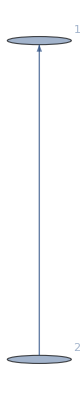

```mathematica
{{2,0},{2,2},{0,2}}//HiggsDecomposition
```

The Residual theory 2 is the origin theory.

The Residual theory 1 is empty, which is the complete Higgsing phase.

The Higgs branch is the isolated singulairty a_2

{Tranverse Theory,Transverse Hypers,Magentic SNF,Residual Theory}= ({{}} | {} | {{2,0},{0,2}} | {{2,0},{2,2},{0,2}}
{{0,2},{2,2}} | {1,2} | {{2,0}} | {{2}}
{{2,-2},{0,2}} | {1,3} | {{2,0}} | {{2}}
{{2,2},{0,2}} | {2,3} | {{2,0}} | {{2}}
{{2,0},{2,2},{0,2}} | {1,2,3} | {{}} | {{}})

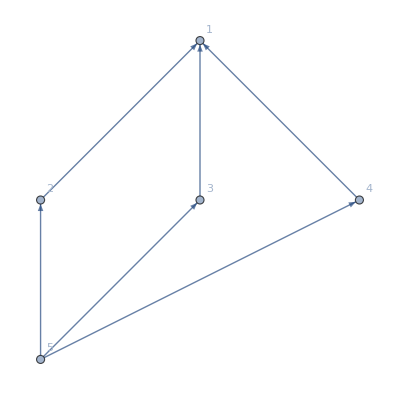

```mathematica
{{2,0},{2,2},{0,2}}//CoulombDecomposition
```

The Residual theory 5 is the origin theory.

The Residual theory 4 is the U(1) theory with charge matrix {{2}}, with the third hyper

The Residual theory 3 is the U(1) theory with charge matrix {{2}}, with the second hyper

The Residual theory 2 is the U(1) theory with charge matrix {{2}}, with the first hyper

```mathematica
(*consistency check with simple case of same Coulomb branch*){{1,0},{1,0},{1,1},{1,1},{0,1},{0,1}}//CoulombDecomposition
```

{Tranverse Theory,Transverse Hypers,Magentic SNF,Residual Theory}= ({{}} | {} | {{1,0},{0,1}} | {{1,0},{1,0},{1,1},{1,1},{0,1},{0,1}}
{{0,1},{0,1},{1,1},{1,1}} | {1,2,3,4} | {{1,0}} | {{1},{1}}
{{1,-1},{1,-1},{0,1},{0,1}} | {1,2,5,6} | {{1,0}} | {{1},{1}}
{{1,1},{1,1},{0,1},{0,1}} | {3,4,5,6} | {{1,0}} | {{1},{1}}
{{1,0},{1,0},{1,1},{1,1},{0,1},{0,1}} | {1,2,3,4,5,6} | {{}} | {{}})

-Graphics-

#### (U(1))^2 with (2 | 0 2 | 0 2 | 2 0 | 2 0 | 2)

```mathematica
{{2,0},{2,0},{2,2},{0,2},{0,2}}//MatrixForm
```

(2 | 0
2 | 0
2 | 2
0 | 2
0 | 2)

{Residual Theory,Residual Hypers,Magentic SNF,Tranverse Theory}= ({{}} | {} | {{2,0},{0,2}} | {{2,0},{2,0},{2,2},{0,2},{0,2}}
{{0,2},{0,2},{2,2}} | {1,2,3} | {{2,0}} | {{2},{2}}
{{2,2},{0,2},{0,2}} | {3,4,5} | {{2,0}} | {{2},{2}}
{{2,0},{2,0},{2,2},{0,2},{0,2}} | {1,2,3,4,5} | {{}} | {{}})

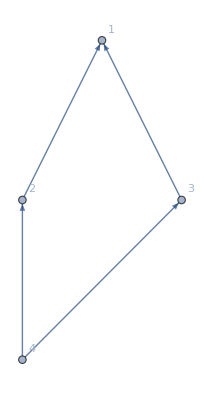

```mathematica
{{2,0},{2,0},{2,2},{0,2},{0,2}}//HiggsDecomposition
```

The Residual theory 4 is the origin theory.

The Residual theory 3 is the Z_2*U(1) theory with combined charge matrix {{0,2},{0,2},{2,2}}, with the 1,2,3 hyper; Which is equivalent to U(1) theory with charge matrix {{1},{1},{1}}

The Residual theory 3 is the Z_2*U(1) theory with combined charge matrix {{2,2},{0,2},{0,2}}, with the 3,4,5 hyper; Which is equivalent to U(1) theory with charge matrix {{1},{1},{1}}

The Residual theory 1 is empty, which is the complete Higgsing phase.

```mathematica
{{2,0},{2,0},{2,2},{0,2},{0,2}}//CoulombDecomposition
```

{Tranverse Theory,Transverse Hypers,Magentic SNF,Residual Theory}= ({{}} | {} | {{2,0},{0,2}} | {{2,0},{2,0},{2,2},{0,2},{0,2}}
{{0,2},{0,2},{2,2}} | {1,2,3} | {{2,0}} | {{2},{2}}
{{2,2},{0,2},{0,2}} | {3,4,5} | {{2,0}} | {{2},{2}}
{{2,-2},{2,-2},{0,2},{0,2}} | {1,2,4,5} | {{2,0}} | {{2}}
{{2,0},{2,0},{2,2},{0,2},{0,2}} | {1,2,3,4,5} | {{}} | {{}})

-Graphics-

#### Z_156*Z_2*Z_2 with (-21 | -2 | -16 8 | 1 | 6 9 | 1 | 7)

(-21 | -2 | -16
8 | 1 | 6
9 | 1 | 7)

{Residual Theory,Residual Hypers,Magentic SNF,Tranverse Theory}= ({{}} | {} | {{1,0,0},{0,1,0},{0,0,1}} | {{-21,-2,-16},{8,1,6},{9,1,7}}
{{-21,-2,5}} | {1} | {{1,0,0},{0,1,0},{0,0,2}} | {{8,1,-2},{9,1,-2}}
{{14,1,-53}} | {2} | {{1,0,0},{0,1,0},{0,0,6}} | {{-37,-2,138},{16,1,-60}}
{{9,1,7}} | {3} | {{1,0,0},{0,1,0},{0,0,2}} | {{-21,-2,-16},{8,1,6}}
{{-16,-13,-27},{6,5,10}} | {1,2} | {{1,0,0},{0,2,0},{0,0,6}} | {{7,6,12}}
{{-39,37,-53},{17,-16,23}} | {1,3} | {{1,0,0},{0,2,0},{0,0,4}} | {{15,-14,20}}
{{15,1,-56},{17,1,-63}} | {2,3} | {{1,0,0},{0,2,0},{0,0,6}} | {{-39,-2,144}}
{{-39,-2,177},{15,1,-86},{17,1,-87}} | {1,2,3} | {{2,0,0},{0,2,0},{0,0,156}} | {{}})

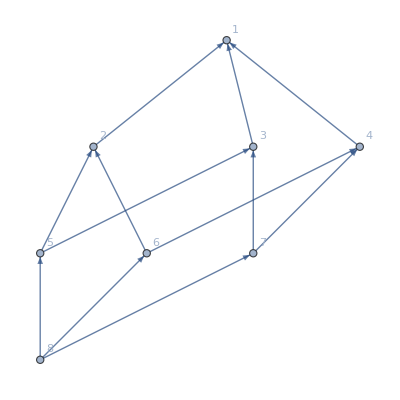

```mathematica
{{-21,-2,-16},{8,1,6},{9,1,7}}//MatrixForm
DiscreteHiggsDecomposition[{{-21,-2,-16},{8,1,6},{9,1,7}},{{156,0,0},{0,2,0},{0,0,2}}]
```

The Residual theory 8 is the origin theory.

The Residual theory 5 is the Z_2*Z_6 theory with charge matrix {{1,-56},{1,-63}}, with 2,3 hyper;

The Residual theory 6 is the Z_2*Z_4 theory with charge matrix {{37,-53},{-16,23}}, with 1,3 hyper;

The Residual theory 5 is the Z_2*Z_6 theory with charge matrix {{-13,-27},{5,6}}, with 1,2 hyper;

The Residual theory 4 is the Z_2 theory with charge matrix {{7}}, with 3rd hyper;

The Residual theory 3 is the Z_6 theory with charge matrix {{-53}}, with 2nd hyper;

The Residual theory 2 is the Z_2 theory with charge matrix {{5}}, with 1st hyper;

The Residual theory 1 is empty, which is the complete Higgsing phase.

### Consistency check with same Coulomb branches

```mathematica
{{3,0},{2,2},{0,4}}//CoulombDecomposition
{{1,0},{2,0},{2,2},{0,4}}//CoulombDecomposition
{{1,0},{2,0},{2,2},{0,2},{0,2}}//CoulombDecomposition
{{1,0},{2,0},{1,1},{1,1},{0,2},{0,2}}//CoulombDecomposition
```

{Tranverse Theory,Transverse Hypers,Magentic SNF,Residual Theory}= ({{}} | {} | {{1,0},{0,2}} | {{3,0},{2,2},{0,4}}
{{0,3},{2,2}} | {1,2} | {{4,0}} | {{4}}
{{3,-3},{0,4}} | {1,3} | {{2,0}} | {{2}}
{{2,2},{0,4}} | {2,3} | {{3,0}} | {{3}}
{{3,0},{2,2},{0,4}} | {1,2,3} | {{}} | {{}})

-Graphics-

{Tranverse Theory,Transverse Hypers,Magentic SNF,Residual Theory}= ({{}} | {} | {{1,0},{0,2}} | {{1,0},{2,0},{2,2},{0,4}}
{{2,2},{0,4}} | {3,4} | {{1,0}} | {{1},{2}}
{{0,1},{0,2},{2,2}} | {1,2,3} | {{4,0}} | {{4}}
{{1,-1},{2,-2},{0,4}} | {1,2,4} | {{2,0}} | {{2}}
{{1,0},{2,0},{2,2},{0,4}} | {1,2,3,4} | {{}} | {{}})

-Graphics-

{Tranverse Theory,Transverse Hypers,Magentic SNF,Residual Theory}= ({{}} | {} | {{1,0},{0,2}} | {{1,0},{2,0},{2,2},{0,2},{0,2}}
{{0,1},{0,2},{2,2}} | {1,2,3} | {{2,0}} | {{2},{2}}
{{2,2},{0,2},{0,2}} | {3,4,5} | {{1,0}} | {{1},{2}}
{{1,-1},{2,-2},{0,2},{0,2}} | {1,2,4,5} | {{2,0}} | {{2}}
{{1,0},{2,0},{2,2},{0,2},{0,2}} | {1,2,3,4,5} | {{}} | {{}})

-Graphics-

{Tranverse Theory,Transverse Hypers,Magentic SNF,Residual Theory}= ({{}} | {} | {{1,0},{0,1}} | {{1,0},{2,0},{1,1},{1,1},{0,2},{0,2}}
{{0,1},{0,2},{1,1},{1,1}} | {1,2,3,4} | {{2,0}} | {{2},{2}}
{{1,-1},{2,-2},{0,2},{0,2}} | {1,2,5,6} | {{1,0}} | {{1},{1}}
{{1,1},{1,1},{0,2},{0,2}} | {3,4,5,6} | {{1,0}} | {{1},{2}}
{{1,0},{2,0},{1,1},{1,1},{0,2},{0,2}} | {1,2,3,4,5,6} | {{}} | {{}})

-Graphics-

```mathematica
{{2,0}}//CoulombDecomposition
{{2,4}}//CoulombDecomposition
{{6,2}}//CoulombDecomposition
{{3,1},{3,1}}//CoulombDecomposition
```

{Tranverse Theory,Transverse Hypers,Magentic SNF,Residual Theory}= ({{}} | {} | {{2,0}} | {{2,0}}
{{2,0}} | {1} | {{}} | {{}})

-Graphics-

{Tranverse Theory,Transverse Hypers,Magentic SNF,Residual Theory}= ({{}} | {} | {{2,0}} | {{2,0}}
{{2,4}} | {1} | {{}} | {{}})

-Graphics-

{Tranverse Theory,Transverse Hypers,Magentic SNF,Residual Theory}= ({{}} | {} | {{2,0}} | {{2,0}}
{{6,2}} | {1} | {{}} | {{}})

-Graphics-

{Tranverse Theory,Transverse Hypers,Magentic SNF,Residual Theory}= ({{}} | {} | {{1,0}} | {{1,0},{1,0}}
{{3,1},{3,1}} | {1,2} | {{}} | {{}})

-Graphics-

```mathematica
{{2,1}}//CoulombDecomposition
{{2,3}}//CoulombDecomposition
{{6,5}}//CoulombDecomposition
```

{Tranverse Theory,Transverse Hypers,Magentic SNF,Residual Theory}= ({{}} | {} | {{}} | {0})

-Graphics-

{Tranverse Theory,Transverse Hypers,Magentic SNF,Residual Theory}= ({{}} | {} | {{}} | {0})

-Graphics-

{Tranverse Theory,Transverse Hypers,Magentic SNF,Residual Theory}= ({{}} | {} | {{}} | {0})

-Graphics-